```mathematica
dir="D:\\workingBuffer 2";
```

```mathematica
dir="D:\\newLight3";
```

```mathematica
indexOfEgg=6;
```

```mathematica
GetNumberOfOrganisms[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nFertile},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms="o"/.items//CountDistinct;
nFertile=Cases[{"o","ct"}/.items,{x_,indexOfEgg}->x]//CountDistinct;
{nOrganisms,nFertile}
]
```

```mathematica
GetCellsPerOrganism[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nCells},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms="o"/.items//CountDistinct;
nCells =items//Length;
nCells/nOrganisms
]
```

```mathematica
f0=0;
fMax=410000;
df=10000;
GetNumberOfOrganisms[fMax]//Print;
frames=Table[f,{f,f0,fMax,df}];
nOrgsList=ParallelMap[GetNumberOfOrganisms,frames]//Transpose;
```

{7153,6330}

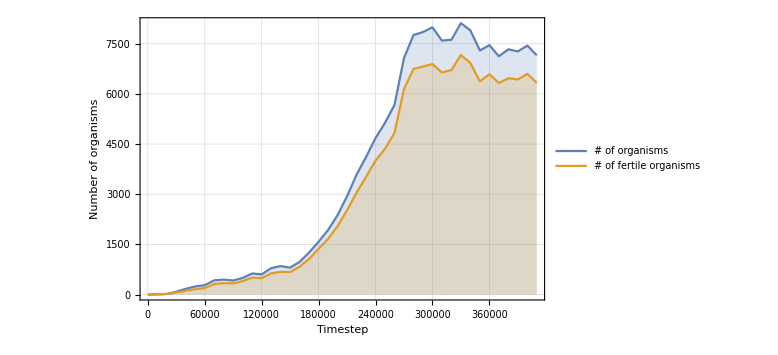

```mathematica
plot=ListPlot[
nOrgsList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
FrameLabel->{"Timestep","Number of organisms"},
PlotLegends->Placed[{"# of organisms","# of fertile organisms"},Above],
ImageSize->Large,
GridLines->Automatic
]
```

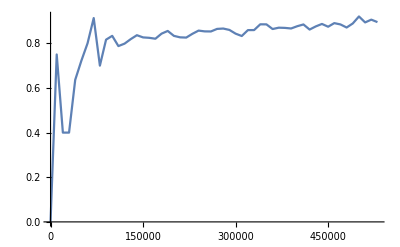

```mathematica
ListLinePlot[(#⟦2⟧)/(#⟦1⟧)&/@Transpose[nOrgsList],DataRange->{f0,fMax}]
```

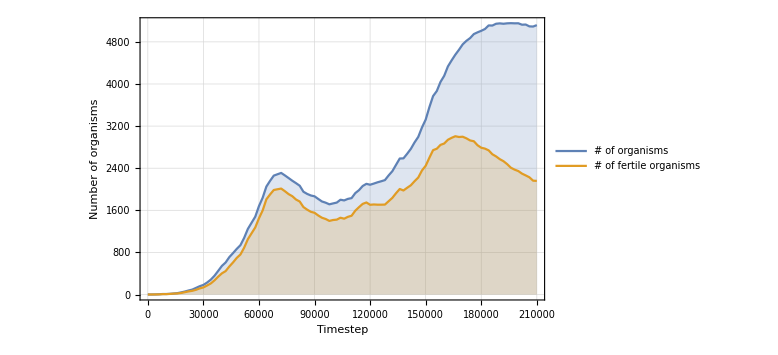

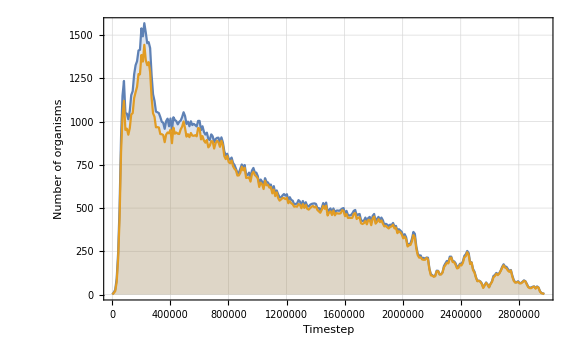

```mathematica
cellFreqList=ParallelMap[GetCellsPerOrganism,frames];
```

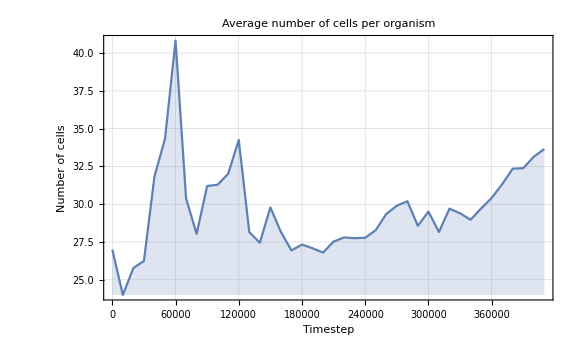

```mathematica
plot2=ListPlot[
cellFreqList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
PlotLabel->"Average number of cells per organism",
FrameLabel->{"Timestep","Number of cells"},
ImageSize->Large,
GridLines->Automatic
]
```